# Chapter. Electrochemistry of strongly adsorbed molecules

In this notebook you are asked to load data from the SERM/Data folder. To prepare for this copy the line below to an input cell, replace the file path with the file path for the "Data" folder on your computer and press ⌤
AppendTo[$Path,”(* path to *)/SERM/Data/chapter11”];
or
AppendTo[$Path,ToFileName[ {NotebookDirectory[],”Data”,”chapter11”}]];

Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"]];
SetSystemOptions["TypesetOptions"->{"IconicElidedForms"->False}];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
Off[InverseFunction::"ifun"];
Off[General::"unfl"];
```

```mathematica
SetOptions[EvaluationNotebook[],
PrintingStartingPageNumber->191,

PageHeaders->{
{Cell[TextData[{CounterBox["Page"]}],FontFamily->"Arial",FontSize->12], Cell[TextData[{"Electrochemistry of Strongly Adsorbed Molecules"}],FontFamily->"Arial",FontSize->12],None},{None,Cell[TextData[CounterBox["Section",CounterFunction:>(Part[{"Introduction","Potential step methods","Constant current methods","Potential sweep methods","Marcus Theory","Further Reading"},#]&)]],FontFamily->"Arial",FontSize->12], Cell[TextData[{CounterBox["Page"]}],FontFamily->"Arial",FontSize->12]}},

PageFooters->{{None,None,None},{None,None,None}},
PrintingOptions-> {
"PrintingMargins"->{{90,90},{60,90}},
"PaperSize"->{596,794},
"PageSize"->{596,794},
"PageHeaderMargins"->{60,60},
"PageFooterMargins"->{30,30},
"GraphicsPrintingFormat"->"DownloadPostScript",
"FirstPageFace"->Right,
"FirstPageHeader"->False,
"FirstPageFooter"->False,
"PrintRegistrationMarks"-> False}];
```

```mathematica
Needs["Notation`"];(*allows the creation of new symbols*)
```

```mathematica
ClearNotations[];
Symbolize[Subscript[x, _]];
Symbolize[Subscript[k, _]];
Symbolize[Subscript[ψ, _]];
Symbolize[𝔼^_];
Symbolize[Subscript[m, _]];
Symbolize[Subscript[Δx, _]];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
BaseStyle->Directive[FontFamily-> "Arial",10,Plain],
Frame->True,
FrameStyle->{Black,AbsoluteThickness[.5]},
GridLines->None,
ImageSize->288,
PlotStyle->{Black,AbsoluteThickness[.5]},
Joined->True];
```

```mathematica
SetOptions[Plot,
Axes->False,
BaseStyle->Directive[FontFamily-> "Arial",10,Plain],
Frame->True,
FrameStyle->{Black,AbsoluteThickness[.5]},
GridLines->None,
ImageSize->288,
PlotStyle->{Black,AbsoluteThickness[.5]}];
```

```mathematica
(* tick function for labelled axes or frames *)
ticks1[min_,max_,steps_,divs_]:=Join[Table[{x,Which[
Chop[x]==0,0,
0<x<2,NumberForm[x,{2,2},NumberPadding->{"","0"}],
x≥2,NumberForm[x,{2,0},NumberPadding->{"","0"}],
0>x≥-2,NumberForm[x,{2,2},NumberPadding->{"0","0"}],
-2>x,NumberForm[x,{2,0},NumberPadding->{"","0"}]
],{0.015,0}},{x,min,max,steps}],Table[{x,"",{0.0075,0}},{x,min,max,steps/divs}]];

ticks1a[min_,max_,steps_,divs_]:=Join[Table[{x,Which[
Chop[x]==0,0,
0<x<2,NumberForm[x,{2,1},NumberPadding->{"","0"}],
x≥2,NumberForm[x,{2,0},NumberPadding->{"","0"}],
0>x≥-2,NumberForm[x,{2,1},NumberPadding->{"0","0"}],
-2>x,NumberForm[x,{2,0},NumberPadding->{"","0"}]
],{0.015,0}},{x,min,max,steps}],Table[{x,"",{0.0075,0}},{x,min,max,steps/divs}]];

(* tick function for non-labelled axes or frames *)
ticks2[min_,max_,steps_,divs_]:=Chop[Join[Table[{x,"",{0.015,0}},{x,min,max,steps}],Table[{x,"",{0.0075,0}},{x,min,max,steps/divs}]]];
```

```mathematica
optionA={
FrameTicks->{ticks1[-10,60,5,5],ticks1[0,.3,.05,5],ticks2[-5,60,5,5],ticks2[0,.3,.05,5]},
RotateLabel->False,
FrameLabel->{Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",Italic],Style["ψ", 10,Plain],None,None}
};
```

```mathematica
optionB={
PlotRange->{{-8,20},{0,0.25}},
PlotRegion-> {{.05,.95},{.05,.95}},
RotateLabel->False,
FrameTicks->{ticks1[-20,20,5,5],ticks1[0,.3,.05,5],ticks2[-10,20,5,5],ticks2[0,.3,.05,5]},
FrameLabel->{Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",Italic],Style["ψ",10,Plain,Black],None,None}
};
```

```mathematica
optionC={
PlotRange->{{-10,10},{0,-0.5}},
AxesOrigin->{-10,0},
PlotStyle->{Black,AbsoluteThickness[0.5]},
FrameLabel->{Style["nF/RT(E-E°)",FontFamily->"Times New Roman",Italic],None,None,None}
};
```

```mathematica
optionD={
PlotStyle-> {Blue,AbsoluteThickness[0.5]},
RotateLabel->False,
FrameTicks->{ticks1[-25,10,5,5],ticks1[0,.3,.05,5],ticks2[-25,10,5,5],ticks2[0,.3,.05,5]},
ImageSize-> 360,
FrameLabel->{Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",Italic],Style["ψ",10,Plain],None,None}
};
```

```mathematica
optionE={
PlotRange->{Automatic,{0,12}},
FrameTicks->{ticks1a[-2,2,.5,5],ticks1[0,14,2,4],ticks2[-2,2,.5,5],ticks2[0,14,2,4]},
FrameLabel->{Style["E-E°",FontFamily-> "Times New Roman",Italic],DisplayForm[Row[{Style["log ","TPP"],"(",Subscript[Style["k","TPI"],Style["b","TPP"]],Style["+","TPP"],Subscript[Style["k","TPI"],Style["f","TPP"]],")"}]],None,None}
};
```

```mathematica
$Line=0;
```

Chapter.Section Introduction

We will consider the reduction of a molecule, O, with both O and R bound to the electrode surface

O + ne ⇌ R

The Faradaic current for the reaction of surface bound molecules is

i(t)=n F A(k_b Γ_R-k_f Γ_O)

where k_f and k_b are the forward and backward rates and Γ_O and Γ_R are the surface concentrations of oxidized and reduced molecules that are written that way rather than Γ_R(t) and Γ_O(t) for brevity. The total surface concentration Γ_T, is assumed to be constant during the experiment

Γ_R+Γ_O=Γ_T

Dividing through by Γ_T gives

x_R+x_O=1

where x_i(t), is the mole fraction. The current is also defined as

i(t)=-n F A (d Γ_R)/(d t)=n F A (d Γ_O)/(d t)

which can be rearranged to

i(t)=-n F A Γ_T(d E)/(d t)(d x_R)/(d E)

## Chapter.Section Potential step methods

When the potential is stepped the rate at which the mole fraction of O or R changes is

(d x_O)/(d t)=k_b x_R-k_f x_O

For a potential step both the forward and backward rates are constant since the potential is fixed. Solving eqn (Chapter.EquationNumbered) with the initial condition that as t=0, x_O=x_O_i gives note

```mathematica
ClearAll[Subscript[x, O],t];
DSolve[{Subscript[x, O]'[t]==kb*(1-Subscript[x, O][t])-kf*Subscript[x, O][t],Subscript[x, O][0]== Subscript[x, Oi]},Subscript[x, O][t], t]//Simplify
```

{{x_O[t]→(ⅇ^(-((kb+kf) t)) (kf x_Oi+kb (-1+ⅇ^((kb+kf) t)+x_Oi)))/(kb+kf)}}

This result can be rearranged to give

x_O(t)=k_b/(k_b+k_f)(1-exp(-(k_b+k_f)t_)+x_O_i exp(-(k_b+k_f)t_))

The equilibrium concentration of x_O is given by

x_O_e=k_b/(k_b+k_f)

Therefore after further rearrangement eqn (Chapter.EquationNumbered) becomes

x_O(t)-x_O_i=(x_O_e-x_O_i)(1-exp(-(k_b+k_f)t_))

## Chapter.Section Constant current methods

In deriving the equation for the constant current response it is assumed that the entire potential drop is experienced by the redox centre and there are no interactions between attached molecules. Equation (Chapter.EquationNumbered) can be rearranged as

(d t)/(d E)=-(nFA Γ_T)/i(d x_R)/dE

Therefore when applying a constant current the derivative of time with respect to potential versus potential can be plotted. In order to predict the outcome of such an experiment the current is first made dimensionless.

ψ=i/(nFA Γ_T)RT/nF(d t)/(d E)=-RT/nF(d x_R)/dE

Combining eqns (Chapter.EquationNumbered), (Chapter.EquationNumbered) and (Chapter.EquationNumbered) gives

i=nFA Γ_T k_s(x_R ξ^(1-α)-(1-x_R)ξ^-α)

where

ξ=exp((nF/RT)(E-E°'))

k_b=k_s ξ^(1-α)

and

k_f=k_s ξ^-α

with k_s being the standard rate constant and E°' the formal potential. x_R is a function of time but since E is a function of time x_R is also a function of ξ. Rearranging eqn (Chapter.EquationNumbered) gives note

```mathematica
ClearAll[n,F,A,Subscript[x, R],t,i,Subscript[k, s],ξ,Γ];

Solve[i==n*F*A*Γ*Subscript[k, s]*(ξ^(1-α)*Subscript[x, R][ξ]-ξ^-α*(1-Subscript[x, R][ξ])),Subscript[x, R][ξ]];
Subscript[x, R][ξ]=Subscript[x, R][ξ]/.%
```

{(A F k_s n Γ+i ξ^α)/(A F k_s n Γ (1+ξ))}

Taking the derivative with respect to ξ

```mathematica
dxR=D[Subscript[x, R][ξ],ξ]//Simplify
```

{(-1+(i ξ^(-1+α) (α-ξ+α ξ))/(A F k_s n Γ))/(1+ξ)^2}

Using the chain rule we have

ψ=-RT/nF(d x_R)/dE=-RT/nF dξ/dE(d x_R)/dξ
=-ξ(d x_R)/dξ

Therefore the dimensionless current ψ is

```mathematica
ψ=-ξ*dxR//Apart
```

{ξ/(1+ξ)^2-(i ξ^α (α-ξ+α ξ))/(A F k_s n Γ (1+ξ)^2)}

Under reversible conditions, i.e. large k_s, the second term on right goes to zero so that the equation becomes

ψ=ξ/(1+ξ)^2

This result is also obtained by noting that under reversible conditions

ξ=Γ_O/Γ_R=x_O/x_R

Therefore after substituting eqns (Chapter.EquationNumbered) we have

x_R=1/(1+ξ)

From eqn (Chapter.EquationNumbered) the dimensionless current will be

```mathematica
-ξ*D[1/(1+ξ),ξ]//Simplify
```

ξ/(1+ξ)^2

Therefore rearranging eqn (Chapter.EquationNumbered) we can express the measured parameter d t/dE as

(d t)/dE=-(A Γ_T)/i((n^2 F^2)/RT)ξ/(1+ξ)^2

From eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered) it can be seen that on a plot of the d t/dE versus E the peak will be symmetrical with ψ reaching its maximum value of 0.25 when ξ=1, i.e. when E=E°'. The peak width at half peak height is 90.6/n mV at 25°C.

## Chapter.Section Potential sweep methods

Chapter.Section.Subsection Analytical solution

The difference between the potential sweep and constant current experiments is that in the potential sweep experiment the current varies and dE/dt is held constant. In a potential sweep experiment the potential is

E = E_i+υ  t

where E_i is the initial potential and υ is the sweep rate which is negative for a cathodic sweep and positive for an anodic sweep. It is convenient to express the current in terms of a dimensionless function; therefore after substituting υ=dE/dt into eqn (Chapter.EquationNumbered) further rearrangement gives

i(t)=n F A Γ_T υ(n F)/(R T)ψ

where the dimensionless current ψ, is defined by eqn (Chapter.EquationNumbered). Since dx_R/dE is negative for both cathodic and anodic reactions it follows that from eqn (Chapter.EquationNumbered) that ψ is always positive. The sign of the current is therefore governed by the sign of υ, i.e. dE/dt, which is negative for a cathodic sweep and positive for an anodic sweep.
In deriving the equation for the linear sweep voltammogram it is assumed that the entire potential drop is experienced by the redox centre and there are no interactions between attached molecules. The equations for reversible reactions are the same as the constant current case with the dimensionless current for a reversible reaction given by eqn (Chapter.EquationNumbered). The peak will be symmetrical with ψ reaching its maximum value of 0.25 when ξ=1. The peak width at half peak height is 90.6/n mV at 25°C.
One of the problems in extracting information from experimentally obtained voltammograms is the ubiquitous peak separation that occurs even at very low sweep rates. Theory predicts that the reversible peak potential is equivalent to the formal potential and that anodic and cathodic reversible peak potentials should be identical. This is rarely observed. In cyclic voltammetry the reversible region is defined as the region, bounded on one side by υ→0, in which the peak potentials, E_p, are constant with increasing sweep rates, i.e. dE_p/dυ=0. The point at which the peak potential changes with increasing sweep rate represents the onset of quasi-reversibility. Experimental voltammograms generally exhibit some peak separation at very low sweep rates, Δ E_p≠0, even when satisfying other criteria of reversibility, specifically dE_p/dυ=0. As the sweep rate is increased the reaction becomes quasi-reversible and eventually irreversible.
Re-writing eqn (Chapter.EquationNumbered) gives the Butler-Volmer equation

i(t)=n F A Γ_T k_s(x_R ξ^(1-α)-x_O ξ^-α)

The general equation for the dimensionless current is obtained by combining eqns (Chapter.EquationNumbered)and (Chapter.EquationNumbered)

ψ=m(x_R ξ^(1-α)-x_O ξ^-α)

where m is a dimensionless rate constant given by

m=(RT k_s)/(nF|υ|)

The absolute value of υ has been used in eqn (Chapter.EquationNumbered) for convenience so that ψ is positive for anodic current and negative for cathodic currents. Substituting eqn (Chapter.EquationNumbered) and (Chapter.EquationNumbered) into (Chapter.EquationNumbered) we have

-ξ(d x_R)/dξ=m(x_R ξ^(1-α)-(1-x_R)ξ^-α)

and following the same procedure using x_O gives

ξ(d x_O)/dξ=m((1-x_O)ξ^(1-α)-x_O ξ^-α)

We are left with these two differential equations to solve. Before solving for the quasi-reversible case let’s consider irreversible reactions for a moment. For an irreversible reaction the rate constant is sufficiently small and/or the sweep rate is sufficiently large that m→0 and for a cathodic reaction ξ^-α≫ξ^(1-α) therefore we have

ξ(d x_O)/dξ=-m x_O ξ^-α

Solving for x_O gives

```mathematica
ClearAll[Subscript[x, O],ξ,α,m];
SetAttributes[m,Constant];
SetAttributes[α,Constant];

cathodic=DSolve[ξ*Subscript[x, O]'[ξ]==-m*Subscript[x, O][ξ]*ξ^-α,Subscript[x, O][ξ], ξ]//Simplify
```

{{x_O[ξ]→ⅇ^((m ξ^-α)/α) C[1]}}

At the beginning of the forward sweep x_O→1 for large values of ξ, i.e. potentials a few hundred millivolts more positive than the formal potential. Recalling that the sweep rate υ is negative for a cathodic sweep, the dimensionless constant m is also negative therefore the exponential term approaches one for large values of ξ and it follows that the integration constant 𝕔_1 equals one.

```mathematica
cathodic⟦1,1,2⟧/.{ξ-> Infinity,α-> 0.5}
```

1. C[1]

```mathematica
Subscript[x, O][ξ]=cathodic⟦1,1,2⟧/.C[1]->1
```

ⅇ^((m ξ^-α)/α)

Taking the derivative gives the dimensionless current for a cathodic sweep (m<0) under irreversible conditions

```mathematica
Subscript[ψ, ci]=ξ*D[Subscript[x, O][ξ],ξ]//Simplify
```

-ⅇ^((m ξ^-α)/α) m ξ^-α

ψ_c=- m ξ^-α exp((m ξ^-α)/α)

To study the peak height and position we first take the derivative of ψ_c with respect to ξ and solve for ξ.

```mathematica
D[Subscript[ψ, ci],ξ]

derivSoln=Quiet@Solve[Simplify[D[Subscript[ψ, ci],ξ]==0,m<0&&α>0&&ξ>0],ξ,InverseFunctions->True]
```

ⅇ^((m ξ^-α)/α) m^2 ξ^(-1-2 α)+ⅇ^((m ξ^-α)/α) m α ξ^(-1-α)

{{ξ→(-m/α)^(1/α)}}

Taking logs of both sides of the answer on the right gives the position of the peak

E_p-E°'=RT/αnF ln(-m/α)	for m < 0

The peak height is determined by substituting the result for ξ back into eqn (Chapter.EquationNumbered).

```mathematica
Simplify[irrevPeak=(Subscript[ψ, ci]/.derivSoln)]
```

{-ⅇ^((m ((-m/α)^(1/α))^-α)/α) m ((-m/α)^(1/α))^-α}

This messy output can be simplified using some assumptions:

```mathematica
Simplify[irrevPeak,{m<0,α>0}]
```

{α/ⅇ}

After simplifying the output we find that at the peak ψ_c=α 𝕖^-1 which is 0.18394 for α =0.5. The peak width at half peak height is determined by substituting ψ_c=1/2 α 𝕖^-1 into eqn (Chapter.EquationNumbered).

```mathematica
halfPeak=Quiet@Solve[ Subscript[ψ, ci]==α/(2.*E),ξ,InverseFunctions->True]//Rationalize
```

{{ξ→0.373365^(1/α) (-m/α)^(1/α)},{ξ→4.31107^(1/α) (-m/α)^(1/α)}}

Taking logs of both sides of these two results gives the potentials at which the half peak height occurs. The peak width at half peak height is simply the difference between these two values

```mathematica
Log[halfPeak⟦2,1,2⟧]-Log[halfPeak⟦1,1,2⟧];
Simplify[%,{m<0,α>0}]
```

2.44639/α

nF/RT(E_2-E_1)=2.446/α

The peak height and the peak width at half height are both independent of m, i.e. independent of the standard rate constant for the reaction and independent of the sweep rate. Therefore we expect no differences in the shape of irreversible cathodic peaks having different rate constants.

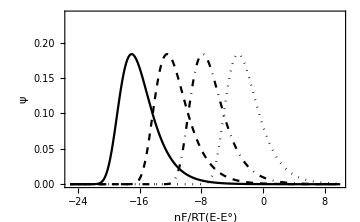

```mathematica
ClearAll[α,ξ,ℰ,m];

α=0.5;
ξ=Exp[ℰ];

Plot[{Evaluate[-ⅇ^((m ξ^-α)/α) m ξ^-α /. m->-0.0001],Evaluate[-ⅇ^((m ξ^-α)/α) m ξ^-α /. m->-0.001],Evaluate[-ⅇ^((m ξ^-α)/α) m ξ^-α /. m->-0.01],Evaluate[-ⅇ^((m ξ^-α)/α) m ξ^-α /. m->-0.1]},{ℰ,-25,10},PlotRange-> {{-25,10}, {0, 0.24}},
PlotStyle->{Black,Directive[Black,Dashed],Directive[Black,DotDashed],Directive[Black,Dotted]},
Evaluate[optionD]]
```

Fig. Chapter.FigureCaption  Plot of irreversible cathodic sweeps calculated from eqn (Chapter.EquationNumbered). From right to left: m=0.1, 0.01, 0.001, 0.0001.

For an irreversible anodic reaction ξ^(1-α)≫ξ^-α therefore:

```mathematica
ClearAll[Subscript[x, R],ξ,α,m];anodic=DSolve[Subscript[x, R]'[ξ]==-m*ξ^-α*Subscript[x, R][ξ],Subscript[x, R][ξ], ξ]//Simplify
```

{{x_R[ξ]→ⅇ^((m ξ^(1-α))/(-1+α)) C[1]}}

```mathematica
Subscript[x, R][ξ]=anodic⟦1,1,2⟧/.C[1]->1
```

ⅇ^((m ξ^(1-α))/(-1+α))

At the beginning of the backward or reverse sweep x_R→1 for very small values of ξ, i.e. potentials a few hundred millivolts more negative than the formal potential, therefore the exponential term approaches one and the integration constant C[1] equals one. The dimensionless current is determined from the derivative of x_R

```mathematica
Subscript[ψ, ai]=-ξ*D[Subscript[x, R][ξ],ξ]//Simplify
```

ⅇ^((m ξ^(1-α))/(-1+α)) m ξ^(1-α)

The dimensionless current for an anodic sweep (m>0) under irreversible conditions is therefore

ψ_a=m ξ^(1-α)exp(-(m ξ^(1-α))/(1-α))	for m>0

The peak potential and the peak width at half peak height can be obtained in the same fashion as for the cathodic peak. We find that the anodic peak potential occurs at

E_p-E°'=RT/((1-α)nF)ln((1-α)/m)	for m>0

The rate constant for the reaction can be determined from the difference, Δ E_p, between the anodic and cathodic peaks in eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered).

logk_s=αlog(1-α)+(1-α)logα-log(RT/nF|υ|)-(α(1-α)nFΔ E_p/2.303RT)

Returning to the quasi-reversible reaction let’s consider firstly the cathodic sweep and solve eqn (Chapter.EquationNumbered).

```mathematica
ClearAll[Subscript[x, R],ξ,α,m];

(*this takes awhile*)
result=DSolve[Subscript[x, R]'[ξ]==-m*(ξ^-α*Subscript[x, R][ξ]-(1-Subscript[x, R][ξ])*ξ^(-1-α)),Subscript[x, R][ξ], ξ,Assumptions->{ξ>0,m∈Reals,α∈Reals,α>0}]//Simplify
```

{{x_R[ξ]→ⅇ^((m ξ^-α (-1+α+α ξ))/((-1+α) α)) (C[1]+ⅇ^(-(m K[1]^-α (-1+α+α K[1]))/((-1+α) α)) m K[1]^(-1-α)K[1]1ξ)}}

For the cathodic sweep we want to integrate between ξ and high positive potentials i.e. ξ→∞. To do this symbolically it is useful to inspect the FullForm of the result where we find a list List[K[1],1,ξ]. The presence of this list can be double checked using Cases.

FullForm@result

```mathematica
Cases[result,{K[1],_,_},∞]
```

{{K[1],1,ξ}}

This allows the integration range to be manually changed.

```mathematica
result=result /. {K[1],_,_}:>{K[1],∞,ξ}
```

{{x_R[ξ]→ⅇ^((m ξ^-α (-1+α+α ξ))/((-1+α) α)) (C[1]+ⅇ^(-(m K[1]^-α (-1+α+α K[1]))/((-1+α) α)) m K[1]^(-1-α)K[1]∞ξ)}}

The symbol K[1] is the display of an internal Mathematica integration variable. For clarity this can be replaced with another symbol.

```mathematica
result1=result/._K-> z
```

{{x_R[ξ]→ⅇ^((m ξ^-α (-1+α+α ξ))/((-1+α) α)) (C[1]+ⅇ^(-(m z^-α (-1+α+z α))/((-1+α) α)) m z^(-1-α)z∞ξ)}}

The integration constant C[1] can be evaluated from the equations for irreversible reactions. For the cathodic reaction when m→0 and the reaction becomes irreversible and at large negative potentials where the peak is found ξ ≪ 1. Therefore (-1+α+αξ)→ (-1+α) so that

(m ξ^-α (-1+α+α ξ))/((-1+α) α)→(m ξ^-α)/α

This replacement can be made to the Mathematica expression. For example:

```mathematica
(-1+α+z α)/.(a_+b_+c_)->  (a+b)
```

-1+α

```mathematica
temp1=result1⟦1,1,2⟧/.(a_+b_+c_)-> (a+b)
```

ⅇ^((m ξ^-α)/α) (C[1]+ⅇ^(-(m z^-α)/α) m z^(-1-α)z∞ξ)

The assumptions can be included in either Simplify or FullSimplify to produce a simplified result. Since these assumptions may be required later on they can be included in a function to simplify the output.

```mathematica
ClearAll[simplify];
simplify[expr_]:=FullSimplify[expr,{ξ>0,m∈Reals,α∈Reals,α>0}]
```

Differentiating the expression for x_R, and multiplying by -ξ gives the dimensionless cathodic current.

```mathematica
-ξ*D[temp1,ξ]
```

-ξ (m ξ^(-1-α)-ⅇ^((m ξ^-α)/α) m ξ^(-1-α) (C[1]+ⅇ^(-(m z^-α)/α) m z^(-1-α)z∞ξ))

This can be equated to the equation for the irreversible cathodic current given in eqn (Chapter.EquationNumbered) and the integration constant C[1] determined and substituted back into the expression for x_R.

```mathematica
tmp=Solve[-ξ*D[temp1,ξ]==Subscript[ψ, ci],C[1]]//simplify
```

{{C[1]→-1+ⅇ^(-(m ξ^-α)/α)-ⅇ^(-(m z^-α)/α) m z^(-1-α)z∞ξ}}

To determine the integration constant we are assuming that m→0:

```mathematica
tmp/.m-> 0
```

{{C[1]→-0z∞ξ}}

An inactive object is returned which can be activated to produce the result.

```mathematica
Activate[tmp/.m-> 0]
```

{{C[1]→0}}

```mathematica
result1=result1/.C[1]->0
```

{{x_R[ξ]→ⅇ^((m ξ^-α (-1+α+α ξ))/((-1+α) α)) ⅇ^(-(m z^-α (-1+α+z α))/((-1+α) α)) m z^(-1-α)z∞ξ}}

Taking the derivative of x_R and multiplying by -ξ gives the dimensionless cathodic current.

```mathematica
Subscript[ψ, c]=-ξ*D[result1⟦1,1,2⟧,ξ]//Simplify
```

m ξ^-α (-1+ⅇ^((m ξ^-α (-1+α+α ξ))/((-1+α) α)) (1+ξ) ⅇ^(-(m z^-α (-1+α+z α))/((-1+α) α)) m z^(-1-α)z∞ξ)

For the anodic reaction we can write

ξ(d x_O)/dξ=m((1-x_O)ξ^(1-α)-x_O ξ^-α)

```mathematica
ClearAll[Subscript[x, O],ξ,α,m];

result2=DSolve[Subscript[x, O]'[ξ]==m*(ξ^-α*(1-Subscript[x, O][ξ])-Subscript[x, O][ξ]*ξ^(-1-α)),Subscript[x, O][ξ], ξ]//Simplify
```

{{x_O[ξ]→ⅇ^((m ξ^-α (-1+α+α ξ))/((-1+α) α)) (C[1]+ⅇ^(-(m K[1]^-α (-1+α+α K[1]))/((-1+α) α)) m K[1]^-αK[1]1ξ)}}

Again the output contains a variable that will appear differently depending on the version of Mathematica you are using. For the anodic sweep we want to integrate between ξ and high negative potentials i.e. 0.

```mathematica
result2=result2/. {K[1],_,_}:>{K[1],0,ξ};
result2=result2/._K-> z
```

{{x_O[ξ]→ⅇ^((m ξ^-α (-1+α+α ξ))/((-1+α) α)) (C[1]+ⅇ^(-(m z^-α (-1+α+z α))/((-1+α) α)) m z^-αz0ξ)}}

The integration constant C[1] can be evaluated from the equation for anodic irreversible reaction. When the anodic reaction becomes irreversible and the peak is found at large positive potentials. Therefore ξ ≫1 and (-1+α+αξ)→ αξ so that (m ξ^-α (-1+α+α ξ))/((-1+α) α)→(m ξ^(1-α))/(-1+α).

```mathematica
(-1+α+α ξ)/.(a_+b_+c_)-> c
```

α ξ

```mathematica
temp2=result2/.(a_+b_+c_)-> c
```

{{x_O[ξ]→ⅇ^((m ξ^(1-α))/(-1+α)) (C[1]+ⅇ^(-(m z^(1-α))/(-1+α)) m z^-αz0ξ)}}

Substituting this into the expression for x_O, then differentiating x_Oand multiplying by ξ gives the dimensionless cathodic current.

```mathematica
ξ*D[temp2⟦1,1,2⟧,ξ]//Simplify
```

m ξ^(1-α) (1-ⅇ^((m ξ^(1-α))/(-1+α)) (C[1]+ⅇ^(-(m z^(1-α))/(-1+α)) m z^-αz0ξ))

Solving for C[1] gives

```mathematica
tmp=Solve[ξ*D[temp2⟦1,1,2⟧,ξ]== Subscript[ψ, ai],C[1]]//simplify
```

{{C[1]→-1+ⅇ^(-(m ξ^(1-α))/(-1+α))-ⅇ^(-(m z^(1-α))/(-1+α)) m z^-αz0ξ}}

```mathematica
Activate[tmp/.m->0]
```

{{C[1]→0}}

The value of C[1] is substituted back into the expression for x_O to give

```mathematica
result2=result2/.C[1]-> 0
```

{{x_O[ξ]→ⅇ^((m ξ^-α (-1+α+α ξ))/((-1+α) α)) ⅇ^(-(m z^-α (-1+α+z α))/((-1+α) α)) m z^-αz0ξ}}

Taking the derivative of x_O and multiplying by ξ gives the dimensionless anodic current.

```mathematica
Subscript[ψ, a]=ξ*D[result2⟦1,1,2⟧,ξ]//FullSimplify
```

m ξ^-α (ξ-ⅇ^((m ξ^-α (-1+α+α ξ))/((-1+α) α)) (1+ξ) ⅇ^(-(m z^-α (-1+α+z α))/((-1+α) α)) m z^-αz0ξ)

Summarizing the equations for the dimensionless current for quasi-reversible reactions:

ψ_c=-mξ^-α(1-m(1+ξ)exp((f(ξ))_)∫_∞^ξ z^(-1-α)exp((-f(z))_)ⅆz)

ψ_a=mξ^-α(ξ-m(1+ξ)exp((f(ξ))_)∫_0^ξ z^-α exp((-f(z))_)ⅆz)

with

f(ξ)=(mξ^-α(α+αξ-1))/((α-1)α)

This analytical solution must be solved numerically. Equations (Chapter.EquationNumbered) and (Chapter.EquationNumbered) could be solved using NIntegrate. Alternatively, since a numerical solution is ultimately required, a more efficient method is to use NDSolve.

### Chapter.Section.Subsection NDSolve solution

Linear sweep voltammograms can be readily generated in Mathematica using NDSolve. To simulate an anodic sweep we can set up the following equation:

(d x_O)/dE=m((1-x_O)ξ^(1-α)-_ x_O ξ^-α)

As an initial condition it is safe to assume that when the dimensionless potential is -10 that the fraction of x_O is zero, i.e. xO[-10]==0. The output is an interpolation function. To plot the voltammogram the interpolated function must first be evaluated using Evaluate

```mathematica
ClearAll[α,m];

α=0.5 (*transfer coefficient*);
m=.01(*rate constant divided by the sweep rate*);
```

```mathematica
ClearAll[Subscript[x, O],ℰ];

potSweep=NDSolve[{Subscript[x, O]'[ℰ]==m*((Exp[(1-α)*ℰ]*(1-Subscript[x, O][ℰ]))-(Exp[-α*ℰ]*Subscript[x, O][ℰ])),Subscript[x, O][-10.]==0.},Subscript[x, O], {ℰ,-10.,20.}]
```

{{x_O→InterpolatingFunction[{{-10.,20.}},<>]}}

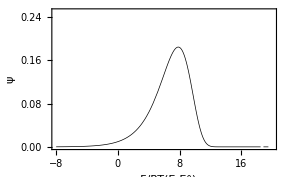

```mathematica
plot1=Plot[Evaluate[Subscript[x, O]'[ℰ]/. potSweep],{ℰ,-8.,20.},Evaluate[optionB]]
```

Fig. Chapter.FigureCaption  Anodic linear sweep voltammogram of a surface bound species. m = 0.01; α = 0.5.

### Chapter.Section.Subsection Finite difference solution

When NDSolve cannot solve the equation to simulate the voltammogram we must use an alternative method. Finite differences makes a good alternative. The sweep can be considered as a series of steps of size ΔE that closely approximates a linear sweep as ΔE→0. Equation (Chapter.EquationNumbered) can be rewritten as

ψ=-RT/nF Δx_R/ΔE=RT/nF Δx_O/ΔE

the magnitude of Δ x_O can be determined from eqn (Chapter.EquationNumbered). Substituting this into eqn (Chapter.EquationNumbered) gives

ψ_(i+1)=RT/nFΔE(x_O_e-x_O_i)(1-exp(-(k_b+k_f)(Δ t)_))

which enables the calculation of the dimensionless current at the  (i+1)th potential step from the values of k_b+k_f at i+1 and the value of x_O at ith step. To convert all variables to a dimensionless form the following substitutions are made

Δτ=nF/RT ΔE

m_i=RT/nF(k_i Δ t)/ΔE

which leads to the equation for the dimensionless current at the (i+1)th step in terms of the dimensionless rates, m_b and m_f, at i+1 and the dimensionless step size Δτ.

ψ_(i+1)=1/Δτ(x_O_e-x_O_i)(1-exp(-(m_b+m_f)Δτ))

```mathematica
ClearAll[α,Subscript[Δx, O],Δe,Subscript[m, s]];

α=0.5; (*transfer coefficient*)
Subscript[Δx, O]=0.; (*Initial value of the incremental fraction oxidized*)
Subscript[m, s]=0.001;(*Dimensionless rate constant*)

increments=600;
lowerLimit=-10.;(*limit = f×(E-E^o)*)
upperLimit=20.;
region=upperLimit+Abs[lowerLimit];
τ=region/increments; (*calculation of the incremental time/potential step*)

ClearAll[Subscript[m, f],Subscript[m, b],j,data];
Subscript[m, f]=Subscript[m, s]*Exp[-α*j*τ];(*forward rate constant*)
Subscript[m, b]=Subscript[m, s]*Exp[(1-α)*j*τ];(*backward rate constant*)
data=Table[{j*τ,Subscript[m, b],Subscript[m, f]},{j,lowerLimit/τ,upperLimit/τ,1}];
```

```mathematica
ClearAll[O1,Subscript[Δx, O],data1];

(*initial value of O1*)
O1=data⟦1,2⟧/(data⟦1,2⟧+data⟦1,3⟧);
Subscript[Δx, O]=0.;
data1=Map[{O1=Subscript[Δx, O]+O1;Subscript[Δx, O]=((#⟦2⟧/(#⟦2⟧+#⟦3⟧))-O1)*(1-Exp[-(#⟦2⟧+#⟦3⟧)*τ]);#⟦1⟧,Subscript[Δx, O]/τ}&,data];
```

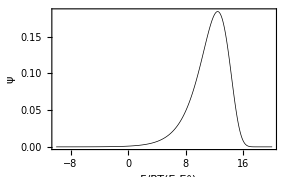

```mathematica
ListPlot[data1,optionA]
```

Fig. Chapter.FigureCaption  Simulated anodic potential sweep. Simulation parameters: m = 0.001; step size= 0.02; α = 0.5.

The peak height and position and peak width at half height can be found from the data. The maximum will be the first element of the output.

```mathematica
ClearAll[z,peakFind,peakWidth,width];

(*find peak maximum*)
z=Max[Map[#⟦2⟧&,data1]];

(*find element corresponding to peak maximum*)
peakFind=Select[data1,#1⟦2⟧==z&];

(*find elements with currents at half maximum. You may need to adjust the search range*)

peakWidth=Select[data1,(1.005*peakFind⟦1,2⟧/2>#1⟦2⟧>0.995*peakFind⟦1,2⟧/2)&];

width=peakWidth⟦1,1⟧-peakWidth⟦2,1⟧(*add widths*);

Print["peak at ",peakFind⟦1,1⟧," with height ",peakFind⟦1,2⟧]
Print["peak width at half maximum is ",Abs[width]]
```

peak at 12.45 with height 0.183928

peak width at half maximum is 4.9

Alternatively the peak can be found by Interpolation.

```mathematica
ClearAll[interpData,peakFind2,peak];

interpData=Interpolation[data1];
peakFind2=Partition[Flatten[FindMinimum[-interpData[ℰ], {ℰ,interpData⟦1,1,1⟧,interpData⟦1,1,2⟧}]],2];

(*peak potential less than .01 is rounded to zero*)
 
peak={Chop[ℰ/. #⟦2⟧,.01],-#⟦1⟧}& /@ peakFind2
```

{{12.4292,0.183938}}

The width at half maximum can be calculated from the interpolation function.

```mathematica
ClearAll[tmp1,tmp2,a,b];

tmp1=peak⟦1,1⟧;
tmp2=0.5*peak⟦1,2⟧;
{a,b}=x/.{FindRoot[interpData[x]==tmp2,{x,0}],FindRoot[interpData[x]==tmp2,{x,13}]}
```

{9.50686,14.3997}

This information can be added to the plot.

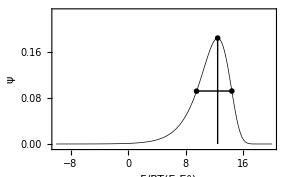

```mathematica
ListPlot[data1,PlotRange->{Automatic,{-.005,.23}},optionA,Epilog-> {Line[{{peak⟦1,1⟧,peak⟦1,2⟧},{peak⟦1,1⟧,0}}],Line[{{a, interpData[a]}, {b, interpData[b]}}],AbsolutePointSize[4],Point/@{peak⟦1⟧,peakWidth⟦1⟧,peakWidth⟦2⟧}}]
```

Fig. Chapter.FigureCaption  Simulated anodic potential sweep. Simulation parameters: m = 0.001; step size= 0.02; α = 0.5.

## Chapter.Section Marcus Theory

The discussions so far have been based on using the Butler-Volmer equation to described the electrode kinetics. The development of self assembled monolayers in which an electroactive centre could be positioned at fixed distances from the electrode has opened up the study of electrochemical reactions that can be used to test Marcus theory. The rate constant for cathodic and anodic reaction, in which there is only a weak electronic coupling between the electrode and the redox centre, is

k_(f,b)=(k_max(RT/(4 πN_A λ)))^(1/2)∫_(-∞)^∞ 1/(1+exp(x))exp{-[(N_A λ±Fη)/RT-x]^2 RT/(4 N_A λ)}ⅆx

where N_A is Avogadro’s constant, λ is the reorganization energy in electron Volts, x is a dimensionless integration variable, and k_max is the maximum value of the rate constant given by

k_max=(4 π^2 ρ H_AB^2)/h

In eqn (Chapter.EquationNumbered) ρ is the density of electronic states in the metal which is assumed to be independent of electrode potential, h is Planck’s constant and H_AB is the electronic coupling matrix element that describes the electronic coupling of reactants electronic state with the products. It is assumed that electronic coupling of less than 50 cm^-1 (0.6 kJ · mol^-1) constitutes weak coupling.
One of the interesting features of this model is that it predicts that the rate constant should reach a constant maximum value at high overpotentials. The magnitude of k_max shows an exponential distance dependency given by

k_max∝exp(-β(d-d_0))

where d_0 is the minimum distance from the redox center to the electrode, and β is a decay constant that depends on the medium through which the electron tunneling occurs. For self assembled monolayers of the alkanethiol type on gold electrodes β is frequently found to be approximately 1.1 Å^-1 per methylene group. The standard rate constant can be determined from eqn (Chapter.EquationNumbered) by setting the overpotential η to zero.

k_s=(k_max(RT/(4 πN_A λ)))^(1/2)∫_(-∞)^∞ 1/(1+exp(x))exp{-[(N_A λ)/RT-x]^2 RT/(4 N_A λ)}ⅆx

Equation (Chapter.EquationNumbered) cannot be solved analytically but a numerical solution is readily available using Mathematica. One possible way of evaluating the integral is to use NIntegrate. After defining all the constants, we get:

```mathematica
ClearAll[η,λ,F,R,T,x];

F=N@QuantityMagnitude@EntityValue[Entity["PhysicalConstant","FaradayConstant"],"Value"];(*Faradays constant*)
R=N@QuantityMagnitude@EntityValue[Entity["PhysicalConstant","MolarGasConstant"],"Value"];(*gas constant*)
T=273.15;(*Absolute temperature*)
λ =.85*F; (*Reorganisation energy*)
η=-1.5;(*overpotential*)
Subscript[k, s]=1.;(*standard rate constant*)
```

```mathematica
NIntegrate[Exp[-(((λ +(F*η))/(R*T))-x)^2*(R*T)/(4*λ)]/(1 + Exp[x]), {x, -Infinity, Infinity}]//Timing
```

{0.010002,21.2864}

An alternative is to use NSum.

```mathematica
NSum[Exp[-(((λ +(F*η))/(R*T))-x)^2*(R*T)/(4*λ)]/(1 + Exp[x]), {x, -Infinity, Infinity},NSumTerms->50]//Timing
```

{0.006941,21.2864}

NSum calculates the first NSumTerms then estimates the rest. To reduce the errors we can increase the option NSumTerms to a higher value. NSum takes longer than NIntegrate the first time it evaluates the integral/sum but it then often faster for any additional calculations where terms outside the integral such as k_max are varied. So to evaluate the rate for a range of k_max values at a given overpotential use NSum but for evaluating the rate at range of overpotentials for a given k_max use NIntegrate.

In the simulations for the remainder of this section we’ll assumed that k_s=1.0  s^-1 and λ=0.85 eV. The first step is to calculate k_max.

```mathematica
y=√((R*T)/(4* λ* Pi))*NSum[Exp[-(λ/(R*T)-x)^2*(R*T)/(4*λ)]/(1 + Exp[x]), {x, -Infinity, Infinity},NSumTerms->50 ];

Subscript[k, max]=Subscript[k, s]/y
```

60042.2

Having calculated k_max we test that the electronic coupling satisfies the assumption of being ‘weak.’

```mathematica
ρ=1.;
h=N@QuantityMagnitude@EntityValue[Entity["PhysicalConstant","PlanckConstant"],"Value"];
e=N@QuantityMagnitude@EntityValue[Entity["PhysicalConstant","ElementaryCharge"],"Value"];
coupling(*coupling in electron volts*)=√((Subscript[k, max]*h)/(4*π^2*e*ρ))
```

2.50796×10^-6

Next step is to generate a list of forward and backward rates over a potential range of -1.5 V to 1.5 V in increments of 1 mV. We need not calculate both forward and backward rates since the term ±η in eqn (Chapter.EquationNumbered) is equal to -|η| so that the rates will mirror each other. The function is compiled so as to speed things up.

```mathematica
ClearAll[η];
rates=Compile[{{min,_Real},{max,_Real},{incr,_Real}},Table[{η,√((R*T)/(4* λ* Pi))*Subscript[k, max]*NIntegrate[Exp[-(((λ +(F*η))/(R*T))-x)^2*(R*T)/(4*λ)]/(1 + Exp[x]), {x, -Infinity, Infinity}]},{η, min,max,incr}]];
```

The function rates calculates the forward rates. The backward rates can then be added.

```mathematica
ClearAll[data];
Timing[data=rates[-1.5,1.5,.5];
back=Reverse[data⟦All,2⟧];
results=MapThread[{#1⟦1⟧,#1⟦2⟧,#2}&,{data,back}]]
```

{0.065784,{{-1.5,59997.3,1.26546×10^-23},{-1.,46135.,1.63471×10^-14},{-0.5,2613.43,1.55567×10^-6},{0.,1.,1.},{0.5,1.55567×10^-6,2613.43},{1.,1.63471×10^-14,46135.},{1.5,1.26546×10^-23,59997.3}}}

The calculation proceeds very slowly but once done can be rapidly repeated for different values of k_max. A plot of the natural logarithm of the rates, calculated from eqn (Chapter.EquationNumbered), versus potential is shown in Fig. Chapter.5.

```mathematica
ClearAll[rates2,logPlot];
rates2=<<marcusRates.dat;
logPlot=Map[{#⟦1⟧,Log[#⟦2⟧+#⟦3⟧]}&,rates2];
```

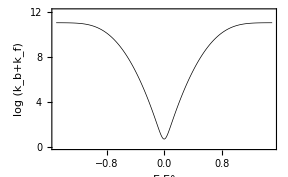

```mathematica
ListPlot[logPlot,optionE]
```

Fig. Chapter.FigureCaption  Plot of ln(k_b+k_f) versus overpotential. Rates calculated with k_s=1.0 s^-1, λ = 0.85 eV and T = 273K.

The rates calculated from Marcus theory can be compared to those calculated from the Butler-Volmer equation. The Butler-Volmer data can be included in the Marcus plot by plotting a line through some calculated Butler-Volmer points and including this line with the command Epilog. In order to help to differentiate the Butler-Volmer data, called bvLogPlot, from the Marcus data in the final plot it would help if the Butler-Volmer line is dashed. This can be achieved with the command line Epilog→{AbsoluteDashing[{3, 3}], Line[bvLogPlot]} inserted into the ListPlot options.

```mathematica
ClearAll[bvRates,bvLogPlot];

bvRates=Table[{η,Subscript[k, s]*Exp[-α*(F*η)/(R*T)],Subscript[k, s]*Exp[(1-α)*(F*η)/(R*T)]},{η, -1.5,1.5, 0.001}];
bvLogPlot=Map[{#⟦1⟧,Log[#⟦2⟧+#⟦3⟧]}&,bvRates];
```

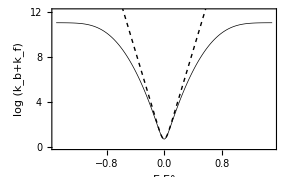

```mathematica
ListPlot[logPlot,optionE,Epilog->{AbsoluteDashing[{3,3}],Line[bvLogPlot]}]
```

Fig. Chapter.FigureCaption  Plot of ln(k_b+k_f) versus overpotential calculated from eqn (Chapter.EquationNumbered) (——) and from the Butler-Volmer equation (-----). Rates calculated with k_s=1.0  s^-1, λ = 0.85  eV and T=273 K.

Note in Fig. Chapter.FigureCaption that when the overpotential is much less than the reorganisation energy there is little difference between the rates calculated from either theory. Solving eqn (Chapter.EquationNumbered) numerically for the forward and backward rates enables the cyclic voltammogram to be simulated using the finite difference approach. The numerical simulation provides information on the factors influencing the shape and position of the peaks.

```mathematica
ClearAll[α,Subscript[Δx, O],data,τ,υ,ff];

α=0.5; (*transfer coefficient*)
Subscript[Δx, O]=0.; (*Initial value of the incremental fraction oxidized*)
τ=.001*F/(R*T);(*calculation of the incremental time/potential step*)
υ=100.;
ff=R*T/(F*υ);

data={#⟦1⟧*F/(R*T),ff*#⟦2⟧,ff*#⟦3⟧}&/@rates2;
```

```mathematica
ClearAll[O1,Subscript[Δx, O],v100];

(*initial value of O1*)
O1=data⟦1,2⟧/(data⟦1,2⟧+data⟦1,3⟧);
Subscript[Δx, O]=0.;
v100=Map[{O1=Subscript[Δx, O]+O1;Subscript[Δx, O]=((#⟦2⟧/(#⟦2⟧+#⟦3⟧))-O1)*(1-Exp[-(#⟦2⟧+#⟦3⟧)*τ]);#⟦1⟧,-Subscript[Δx, O]/τ}&,data];
```

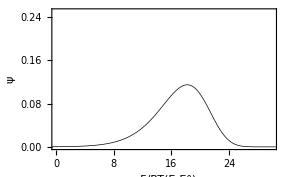

```mathematica
ListPlot[v100,PlotRange->{{0.,30.},{0,0.25}},optionA]
```

Fig. Chapter.FigureCaption  Plot of anodic linear sweep voltammograms. Simulation parameters λ=0.85  eV, T=273 K and k_s/υ=0.01  V^-1.

```mathematica
ClearAll[interpData,peakFind2,peak,halfWidth];

interpData=Interpolation[v100];
peakFind2=Partition[Flatten[FindMinimum[-interpData[ℰ], {ℰ,0,30}]],2];
(*peak potential less than 0.01 is rounded to zero*)
 peak={Chop[ℰ/. #⟦2⟧,0.01],-#⟦1⟧}& /@ peakFind2;

ClearAll[tmp1,tmp2,a,b];
tmp1=peak⟦1,1⟧;
tmp2=0.5*peak⟦1,2⟧;
{a,b}=x/.{FindRoot[interpData[x]==tmp2,{x,5}],FindRoot[interpData[x]==tmp2,{x,peak⟦1,1⟧,peak⟦1,1⟧,30}]};
```

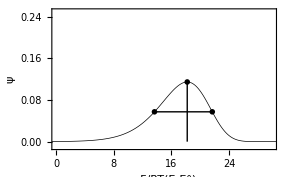

```mathematica
ListPlot[v100,PlotRange->{{0,30},{-.01,.25}},optionA,Epilog-> {Line[{{peak⟦1,1⟧,peak⟦1,2⟧},{peak⟦1,1⟧,0}}],Line[{{a, interpData[a]}, {b, interpData[b]}}],AbsolutePointSize[4],Point/@{peak⟦1⟧,{a,interpData[a]},{b,interpData[b]}}}]
```

Fig. Chapter.FigureCaption  Plot of anodic linear sweep voltammograms. Simulation parameters λ=0.85  eV, T=273 K and k_s/υ=0.01  V^-1. The dimensionless peak height is 0.114 and peak width at half height is 8.0.

While eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered), based on Butler-Volmer kinetics, predicts that the irreversible peak shape should be a constant asymmetric shape, the model based on Marcus theory predicts the peak shape to be dependent on λ, the reorganisation energy, and the peak shape should change with increasing sweep rate. This is a key difference between the two models. Below in Fig. Chapter.FigureCaption are five linear sweep voltammograms using the same parameters as in Fig Chapter.FigureCaption but with different sweep rates. The data has been saved and recalled to enable the five plots to be displayed together.

```mathematica
ClearAll[v1,v10,v100,v1000,v10000];

v1=<<v1.dat;
v10=<<v10.dat;
v100=<<v100.dat;
v1000=<<v1000.dat;
v10000=<<v10000.dat;
```

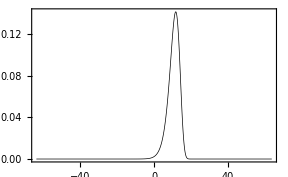

```mathematica
ListPlot[v10,PlotRange->All]
```

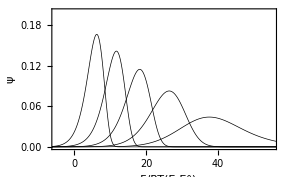

```mathematica
Show[
ListPlot[v1,PlotRange->{{-5.,55.},{0,0.2}},optionA],ListPlot[v10,PlotRange->{{-5.,55.},{0,0.2}}],ListPlot[v100,PlotRange->{{-5.,55.},{0,0.2}}],ListPlot[v1000,PlotRange->{{-5.,55.},{0,0.2}}],ListPlot[v10000]]
```

Fig. Chapter.FigureCaption  Plots of anodic linear sweep voltammograms. Simulation parameters λ=0.85 eV and T=273 K and from left to right k_s/υ=1, 0.1, 0.01, 0.001, 0.0001 V^-1.

As the sweep rate is increased peaks become progressively broader and flatter and at sufficiently high values of Fη/λ the peaks show diffusional type tailing and eventually the determination of E_p becomes difficult. For small to moderate overpotentials the value of k_s obtained from the distance between the anodic and cathodic peaks does not deviate much from that predicted by Butler-Volmer kinetics. On the other hand the peak current is greatly dependent on λ.

## Further Reading

Chidsey, C. D. (1991). Science, 251, 919-22.
Finklea, H. O. (1996). Electrochemistry of Organised Monolayers of Thiols and Related Molecules on Electrodes. In Electroanalytical Chemistry, Vol.19. (eds. A.J.Bard and I.Rubenstein), pp.110-337, Marcel Dekker, New York.
Laviron, E., (1982). Voltammetric Methods for the Study of Adsorbed Species. In Electroanalytical Chemistry, Vol. 12. (ed. A. J. Bard), pp. 53-157, Marcel Dekker, New York .
Levich, V. G. (1970). Kinetics of Reactions with Charge Transport. In Physical Chemistry: An Advanced Treatise, Vol. 9B. (ed. H. Eyring), pp. 985-1074. Academic Press, New York.
Levich, V. G. (1966). Present State of the Theory of Oxidation-Reduction in Solution (Bulk and Electrode Reactions). In Advances in Electrochemistry and Electrochemical Engineering, Vol. 4. (ed. P. Delahay), pp. 249-372. Wiley, New York.
Schmickler, W. (1996). Interfacial Electrochemistry, Oxford University Press, Oxford.